## Mobius and zeta

```mathematica
allVars=Sort[DeleteDuplicates[ListofVars[ineqsW2]]]
```

{n1234,n123x4,n124x3,n12x34,n12x3x4,n134x2,n13x24,n13x2x4,n14x23,n14x2x3,n1x234,n1x23x4,n1x24x3,n1x2x34,n1x2x3x4}

```mathematica
Select[Keys[allGraphs],Length[ListofVars[allGraphs[#,"colofourrealnull"]]]==203&]
```

{}

```mathematica
Permutations[{1,2,3}]
```

{{1,2,3},{1,3,2},{2,1,3},{2,3,1},{3,1,2},{3,2,1}}

```mathematica
vertices={n1234,n123x4,n124x3,n12x34,n134x2,n13x24,n14x23,n1x234,n12x3x4,n13x2x4,n14x2x3,n1x23x4,n1x24x3,n1x2x34,n1x2x3x4};
```

```mathematica
perm=Permutations[{n123x4,n124x3,n12x34,n134x2,n13x24,n14x23,n1x234}];
```

```mathematica
perm2=Permutations[{n12x3x4,n13x2x4,n14x2x3,n1x23x4,n1x24x3,n1x2x34}];
```

```mathematica
Length[perm]
```

5040

```mathematica
Length[perm2]
```

720

```mathematica
720*5040
```

3628800

```mathematica
Length[allGraphs]
```

1895

```mathematica
current=0;Select[
Flatten[
Monitor[
Table[
vertices=Join[{n1234},vert,vert2,{n1x2x3x4}];
four=Graph[vertices,Map[#[[2]]->#[[1]]&,AndToTable[Select[ineqsW2,Length[ListofVars[#]]==2&]]],VertexLabels->"Name",GraphLayout->"LayeredDigraphEmbedding"];
IM=IdentityMatrix[Length[VertexList[four]]];
fourM=AdjacencyMatrix[four];
ZetaM=MakeOne[Inverse[IM-fourM]];
MobiusM=Inverse[ZetaM];
If[ZetaM[[2,8]]==1&&ZetaM[[3,8]]==1&&ZetaM[[4,8]]==1&&ZetaM[[5,8]]==1,
Print[vertices];
MatrixPlot[ZetaM,Mesh->{Table[Sum[StirlingS2[6,i],{i,1,k}],{k,1,6}],Table[Sum[StirlingS2[6,i],{i,1,k}],{k,1,6}]},ImageSize->150];
Interrupt[]
];
current++,
{vert,perm},{vert2,Take[perm2,360]}
],{current}
]]
,#≠Null&]
```

Flatten::normal: Nonatomic expression expected at position 1 in Flatten[$Aborted].

Flatten::argb: Flatten called with 0 arguments; between 1 and 3 arguments are expected.

Flatten[]

```mathematica
Length[allGraphs]
```

127

```mathematica
Det[MobiusM]
```

1

```mathematica
ZetaM[[4,8]]=0
```

0

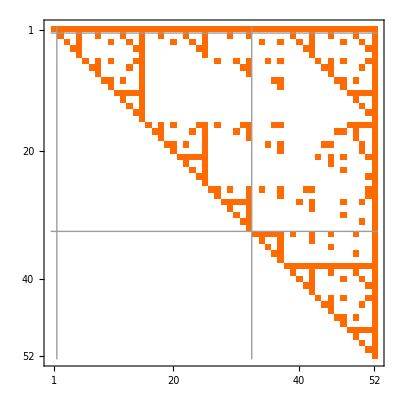

```mathematica
MatrixPlot[ZetaM,Mesh->{Table[Sum[StirlingS2[6,i],{i,1,k}],{k,1,6}],Table[Sum[StirlingS2[6,i],{i,1,k}],{k,1,6}]}]
```

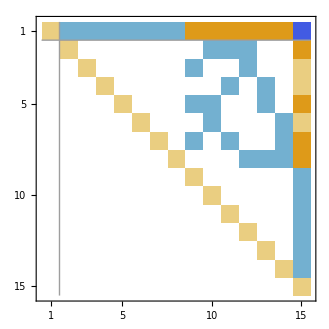

```mathematica
MatrixPlot[MobiusM,Mesh->{Table[Sum[StirlingS2[6,i],{i,1,k}],{k,1,6}],Table[Sum[StirlingS2[6,i],{i,1,k}],{k,1,6}]}]
```

```mathematica
Mob=Association[]
```

<||>

```mathematica
Length[VertexList[four]]
```

15

```mathematica
MobiusM[[5]]
```

{0,0,0,0,1,0,0,0,-1,-1,0,0,-1,0,2}

```mathematica
With[{l=VertexList[four]},
Table[Mob[l[[k]]]=MobiusM[[Length[l],k]],{k,1,Length[l]}]
]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,1}

```mathematica
Gr=Association[];With[{l=VertexList[four]},
Table[Gr[l[[k]]]=allGraphs[First[Select[Keys[allGraphs],allGraphs[#,"colofourrealnull"]==l[[k]]&]],"vertexsets"],{k,1,Length[l]}]
]
```

{{{1,2,3,4}},{{1},{2,3,4}},{{1,4},{2,3}},{{1,3},{2,4}},{{1,3,4},{2}},{{1,2},{3,4}},{{1,2,4},{3}},{{1,2,3},{4}},{{1,4},{2},{3}},{{1},{2},{3,4}},{{1},{2,4},{3}},{{1},{2,3},{4}},{{1,3},{2},{4}},{{1,2},{3},{4}},{{1},{2},{3},{4}}}

```mathematica
Gr2=Association[];With[{l=VertexList[four]},
Table[Gr2[l[[k]]]=allGraphs[First[Select[Keys[allGraphs],allGraphs[#,"colofourrealnull"]==l[[k]]&]]],{k,1,Length[l]}]
];
```

```mathematica
Graph[vertices,Map[#[[2]]->#[[1]]&,AndToTable[Select[ineqsW2,Length[ListofVars[#]]==2&]]],VertexLabels->Table[v->Rotate[ToString[Gr[v]],Pi/4]->Mob[v],{v,VertexList[four]}],GraphLayout->"TutteEmbedding",DirectedEdges->False]
```

```mathematica
Graph[vertices,Map[#[[2]]->#[[1]]&,AndToTable[Select[ineqsW2,Length[ListofVars[#]]==2&]]],VertexLabels->Table[v->Mob[v],{v,VertexList[four]}],GraphLayout->"TutteEmbedding",DirectedEdges->False]
```

```mathematica
Take[Table[{Gr2[v,"graph"],v,Gr[v],Mob[v],4^Length[Gr[v]],FactorInteger[Mob[v]*4^Length[Gr[v]]]},{v,VertexList[four]}],3]
```

{{-Graphics-,n1234,{{1,2,3,4}},0,4,{{0,1}}},{-Graphics-,n1x234,{{1},{2,3,4}},0,16,{{0,1}}},{-Graphics-,n14x23,{{1,4},{2,3}},0,16,{{0,1}}}}

```mathematica
TableForm[Sort[Table[{Gr2[v,"graph"],v,Gr[v],Mob[v],4^Length[Gr[v]],Mob[v]*4^Length[Gr[v]],FactorInteger[Mob[v]*4^Length[Gr[v]]]},{v,VertexList[four]}],Abs[#1[[4]]]>Abs[#2[[4]]]&],TableDepth->2]
```

-Graphics- | n1x2x3x4 | {{1},{2},{3},{4}} | 1 | 256 | 256 | {{2,8}}
-Graphics- | n12x3x4 | {{1,2},{3},{4}} | 0 | 64 | 0 | {{0,1}}
-Graphics- | n13x2x4 | {{1,3},{2},{4}} | 0 | 64 | 0 | {{0,1}}
-Graphics- | n1x23x4 | {{1},{2,3},{4}} | 0 | 64 | 0 | {{0,1}}
-Graphics- | n1x24x3 | {{1},{2,4},{3}} | 0 | 64 | 0 | {{0,1}}
-Graphics- | n1x2x34 | {{1},{2},{3,4}} | 0 | 64 | 0 | {{0,1}}
-Graphics- | n14x2x3 | {{1,4},{2},{3}} | 0 | 64 | 0 | {{0,1}}
-Graphics- | n123x4 | {{1,2,3},{4}} | 0 | 16 | 0 | {{0,1}}
-Graphics- | n124x3 | {{1,2,4},{3}} | 0 | 16 | 0 | {{0,1}}
-Graphics- | n12x34 | {{1,2},{3,4}} | 0 | 16 | 0 | {{0,1}}
-Graphics- | n134x2 | {{1,3,4},{2}} | 0 | 16 | 0 | {{0,1}}
-Graphics- | n13x24 | {{1,3},{2,4}} | 0 | 16 | 0 | {{0,1}}
-Graphics- | n14x23 | {{1,4},{2,3}} | 0 | 16 | 0 | {{0,1}}
-Graphics- | n1x234 | {{1},{2,3,4}} | 0 | 16 | 0 | {{0,1}}
-Graphics- | n1234 | {{1,2,3,4}} | 0 | 4 | 0 | {{0,1}}

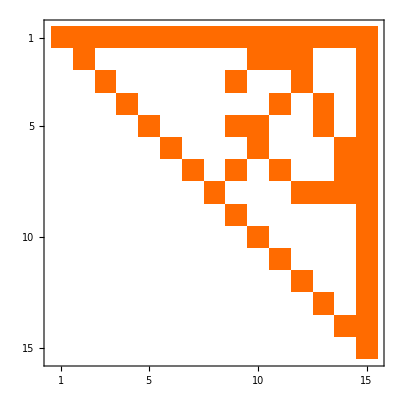

```mathematica
ZetaM//MatrixPlot
```

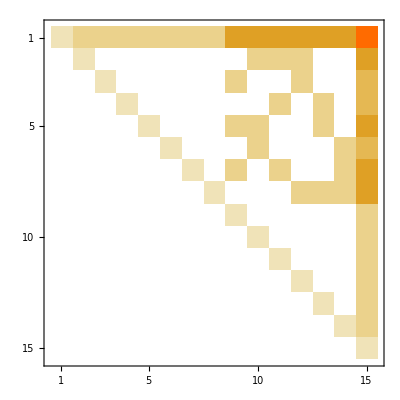

```mathematica
MatrixPower[ZetaM,2]//MatrixPlot
```

```mathematica
Table[MatrixPower[ZetaM,k]//MatrixForm,{k,0,10}]
```

{(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1),(1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 0 | 0 | 1
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 1
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 1
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 1 | 0 | 1
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 1
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 1 | 0 | 0 | 1 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 1 | 1 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1),(1 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 5 | 5 | 5 | 5 | 5 | 5 | 15
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 2 | 2 | 0 | 0 | 5
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 2 | 0 | 0 | 4
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 2 | 0 | 4
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 2 | 2 | 0 | 0 | 2 | 0 | 5
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 2 | 4
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 2 | 0 | 2 | 0 | 0 | 2 | 5
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 2 | 2 | 2 | 5
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 2
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 2
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 2
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 2
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 2
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 2
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1),(1 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 12 | 12 | 12 | 12 | 12 | 12 | 60
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3 | 3 | 3 | 0 | 0 | 12
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 3 | 0 | 0 | 3 | 0 | 0 | 9
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 3 | 0 | 3 | 0 | 9
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 3 | 3 | 0 | 0 | 3 | 0 | 12
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 3 | 0 | 0 | 0 | 3 | 9
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 3 | 0 | 3 | 0 | 0 | 3 | 12
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 3 | 3 | 3 | 12
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 3
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 3
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 3
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 3
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 3
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 3
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1),(1 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 22 | 22 | 22 | 22 | 22 | 22 | 154
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 4 | 4 | 4 | 0 | 0 | 22
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 4 | 0 | 0 | 4 | 0 | 0 | 16
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 4 | 0 | 4 | 0 | 16
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 4 | 4 | 0 | 0 | 4 | 0 | 22
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 4 | 0 | 0 | 0 | 4 | 16
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 4 | 0 | 4 | 0 | 0 | 4 | 22
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 4 | 4 | 4 | 22
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 4
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 4
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 4
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 4
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 4
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 4
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1),(1 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 35 | 35 | 35 | 35 | 35 | 35 | 315
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 5 | 5 | 5 | 0 | 0 | 35
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 5 | 0 | 0 | 5 | 0 | 0 | 25
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 5 | 0 | 5 | 0 | 25
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 5 | 5 | 0 | 0 | 5 | 0 | 35
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 5 | 0 | 0 | 0 | 5 | 25
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 5 | 0 | 5 | 0 | 0 | 5 | 35
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 5 | 5 | 5 | 35
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 5
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 5
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 5
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 5
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 5
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 5
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1),(1 | 6 | 6 | 6 | 6 | 6 | 6 | 6 | 51 | 51 | 51 | 51 | 51 | 51 | 561
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 6 | 6 | 6 | 0 | 0 | 51
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 6 | 0 | 0 | 6 | 0 | 0 | 36
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 6 | 0 | 6 | 0 | 36
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 6 | 6 | 0 | 0 | 6 | 0 | 51
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 6 | 0 | 0 | 0 | 6 | 36
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 6 | 0 | 6 | 0 | 0 | 6 | 51
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 6 | 6 | 6 | 51
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 6
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 6
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 6
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 6
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 6
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 6
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1),(1 | 7 | 7 | 7 | 7 | 7 | 7 | 7 | 70 | 70 | 70 | 70 | 70 | 70 | 910
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 7 | 7 | 7 | 0 | 0 | 70
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 7 | 0 | 0 | 7 | 0 | 0 | 49
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 7 | 0 | 7 | 0 | 49
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 7 | 7 | 0 | 0 | 7 | 0 | 70
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 7 | 0 | 0 | 0 | 7 | 49
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 7 | 0 | 7 | 0 | 0 | 7 | 70
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 7 | 7 | 7 | 70
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 7
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 7
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 7
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 7
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 7
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 7
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1),(1 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 92 | 92 | 92 | 92 | 92 | 92 | 1380
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 8 | 8 | 8 | 0 | 0 | 92
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 8 | 0 | 0 | 8 | 0 | 0 | 64
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 8 | 0 | 8 | 0 | 64
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 8 | 8 | 0 | 0 | 8 | 0 | 92
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 8 | 0 | 0 | 0 | 8 | 64
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 8 | 0 | 8 | 0 | 0 | 8 | 92
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 8 | 8 | 8 | 92
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 8
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 8
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 8
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 8
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 8
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 8
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1),(1 | 9 | 9 | 9 | 9 | 9 | 9 | 9 | 117 | 117 | 117 | 117 | 117 | 117 | 1989
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 9 | 9 | 9 | 0 | 0 | 117
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 9 | 0 | 0 | 9 | 0 | 0 | 81
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 9 | 0 | 9 | 0 | 81
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 9 | 9 | 0 | 0 | 9 | 0 | 117
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 9 | 0 | 0 | 0 | 9 | 81
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 9 | 0 | 9 | 0 | 0 | 9 | 117
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 9 | 9 | 9 | 117
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 9
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 9
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 9
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 9
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 9
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 9
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1),(1 | 10 | 10 | 10 | 10 | 10 | 10 | 10 | 145 | 145 | 145 | 145 | 145 | 145 | 2755
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 10 | 10 | 10 | 0 | 0 | 145
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 10 | 0 | 0 | 10 | 0 | 0 | 100
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 10 | 0 | 10 | 0 | 100
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 10 | 10 | 0 | 0 | 10 | 0 | 145
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 10 | 0 | 0 | 0 | 10 | 100
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 10 | 0 | 10 | 0 | 0 | 10 | 145
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 10 | 10 | 10 | 145
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 10
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 10
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 10
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 10
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 10
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 10
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1)}

```mathematica
Table[MatrixPower[MobiusM,k]//MatrixForm,{k,0,10}]
```

{(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1),(1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | 2 | 2 | 2 | 2 | 2 | 2 | -6
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | -1 | -1 | 0 | 0 | 2
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | -1 | 0 | 0 | 1
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | -1 | 0 | 1
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | -1 | -1 | 0 | 0 | -1 | 0 | 2
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | -1 | 1
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | -1 | 0 | -1 | 0 | 0 | -1 | 2
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | -1 | -1 | -1 | 2
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1),(1 | -2 | -2 | -2 | -2 | -2 | -2 | -2 | 7 | 7 | 7 | 7 | 7 | 7 | -35
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2 | -2 | -2 | 0 | 0 | 7
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | -2 | 0 | 0 | -2 | 0 | 0 | 4
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | -2 | 0 | -2 | 0 | 4
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | -2 | -2 | 0 | 0 | -2 | 0 | 7
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | -2 | 0 | 0 | 0 | -2 | 4
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | -2 | 0 | -2 | 0 | 0 | -2 | 7
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | -2 | -2 | -2 | 7
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | -2
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | -2
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | -2
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | -2
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | -2
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -2
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1),(1 | -3 | -3 | -3 | -3 | -3 | -3 | -3 | 15 | 15 | 15 | 15 | 15 | 15 | -105
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -3 | -3 | -3 | 0 | 0 | 15
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | -3 | 0 | 0 | -3 | 0 | 0 | 9
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | -3 | 0 | -3 | 0 | 9
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | -3 | -3 | 0 | 0 | -3 | 0 | 15
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | -3 | 0 | 0 | 0 | -3 | 9
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | -3 | 0 | -3 | 0 | 0 | -3 | 15
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | -3 | -3 | -3 | 15
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | -3
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | -3
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | -3
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | -3
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | -3
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -3
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1),(1 | -4 | -4 | -4 | -4 | -4 | -4 | -4 | 26 | 26 | 26 | 26 | 26 | 26 | -234
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -4 | -4 | -4 | 0 | 0 | 26
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | -4 | 0 | 0 | -4 | 0 | 0 | 16
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | -4 | 0 | -4 | 0 | 16
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | -4 | -4 | 0 | 0 | -4 | 0 | 26
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | -4 | 0 | 0 | 0 | -4 | 16
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | -4 | 0 | -4 | 0 | 0 | -4 | 26
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | -4 | -4 | -4 | 26
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | -4
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | -4
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | -4
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | -4
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | -4
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -4
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1),(1 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | 40 | 40 | 40 | 40 | 40 | 40 | -440
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -5 | -5 | -5 | 0 | 0 | 40
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | -5 | 0 | 0 | -5 | 0 | 0 | 25
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | -5 | 0 | -5 | 0 | 25
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | -5 | -5 | 0 | 0 | -5 | 0 | 40
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | -5 | 0 | 0 | 0 | -5 | 25
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | -5 | 0 | -5 | 0 | 0 | -5 | 40
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | -5 | -5 | -5 | 40
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | -5
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | -5
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | -5
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | -5
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | -5
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -5
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1),(1 | -6 | -6 | -6 | -6 | -6 | -6 | -6 | 57 | 57 | 57 | 57 | 57 | 57 | -741
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -6 | -6 | -6 | 0 | 0 | 57
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | -6 | 0 | 0 | -6 | 0 | 0 | 36
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | -6 | 0 | -6 | 0 | 36
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | -6 | -6 | 0 | 0 | -6 | 0 | 57
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | -6 | 0 | 0 | 0 | -6 | 36
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | -6 | 0 | -6 | 0 | 0 | -6 | 57
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | -6 | -6 | -6 | 57
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | -6
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | -6
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | -6
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | -6
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | -6
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -6
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1),(1 | -7 | -7 | -7 | -7 | -7 | -7 | -7 | 77 | 77 | 77 | 77 | 77 | 77 | -1155
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -7 | -7 | -7 | 0 | 0 | 77
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | -7 | 0 | 0 | -7 | 0 | 0 | 49
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | -7 | 0 | -7 | 0 | 49
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | -7 | -7 | 0 | 0 | -7 | 0 | 77
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | -7 | 0 | 0 | 0 | -7 | 49
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | -7 | 0 | -7 | 0 | 0 | -7 | 77
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | -7 | -7 | -7 | 77
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | -7
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | -7
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | -7
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | -7
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | -7
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -7
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1),(1 | -8 | -8 | -8 | -8 | -8 | -8 | -8 | 100 | 100 | 100 | 100 | 100 | 100 | -1700
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -8 | -8 | -8 | 0 | 0 | 100
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | -8 | 0 | 0 | -8 | 0 | 0 | 64
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | -8 | 0 | -8 | 0 | 64
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | -8 | -8 | 0 | 0 | -8 | 0 | 100
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | -8 | 0 | 0 | 0 | -8 | 64
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | -8 | 0 | -8 | 0 | 0 | -8 | 100
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | -8 | -8 | -8 | 100
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | -8
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | -8
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | -8
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | -8
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | -8
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -8
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1),(1 | -9 | -9 | -9 | -9 | -9 | -9 | -9 | 126 | 126 | 126 | 126 | 126 | 126 | -2394
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -9 | -9 | -9 | 0 | 0 | 126
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | -9 | 0 | 0 | -9 | 0 | 0 | 81
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | -9 | 0 | -9 | 0 | 81
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | -9 | -9 | 0 | 0 | -9 | 0 | 126
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | -9 | 0 | 0 | 0 | -9 | 81
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | -9 | 0 | -9 | 0 | 0 | -9 | 126
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | -9 | -9 | -9 | 126
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | -9
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | -9
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | -9
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | -9
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | -9
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -9
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1),(1 | -10 | -10 | -10 | -10 | -10 | -10 | -10 | 155 | 155 | 155 | 155 | 155 | 155 | -3255
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -10 | -10 | -10 | 0 | 0 | 155
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | -10 | 0 | 0 | -10 | 0 | 0 | 100
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | -10 | 0 | -10 | 0 | 100
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | -10 | -10 | 0 | 0 | -10 | 0 | 155
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | -10 | 0 | 0 | 0 | -10 | 100
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | -10 | 0 | -10 | 0 | 0 | -10 | 155
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | -10 | -10 | -10 | 155
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | -10
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | -10
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | -10
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | -10
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | -10
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -10
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1)}

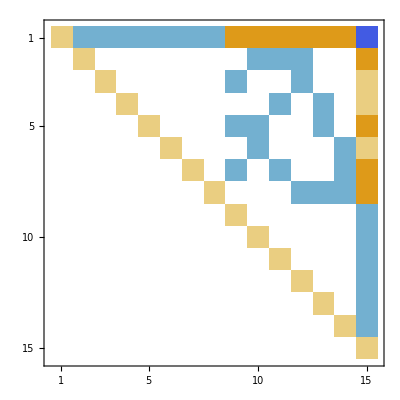

```mathematica
Inverse[ZetaM]//MatrixPlot
```

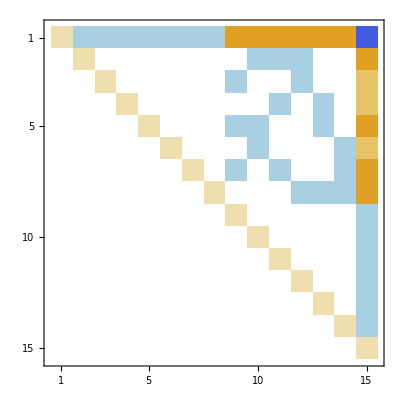

```mathematica
MatrixPower[Inverse[ZetaM],3]//MatrixPlot
```

```mathematica
MatrixPower[Inverse[ZetaM],15]//MatrixForm
```

(1 | -15 | -15 | -15 | -15 | -15 | -15 | -15 | 345 | 345 | 345 | 345 | 345 | 345 | -10695
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -15 | -15 | -15 | 0 | 0 | 345
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | -15 | 0 | 0 | -15 | 0 | 0 | 225
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | -15 | 0 | -15 | 0 | 225
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | -15 | -15 | 0 | 0 | -15 | 0 | 345
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | -15 | 0 | 0 | 0 | -15 | 225
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | -15 | 0 | -15 | 0 | 0 | -15 | 345
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | -15 | -15 | -15 | 345
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | -15
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | -15
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | -15
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | -15
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | -15
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -15
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1)

```mathematica
Subgraph
```

Subgraph

```mathematica
GraphZeta[g_]:=Block[{ordered=TopologicalSort[four]},
Table[If[ToString[i]==ToString[j]||EdgeQ[g,i->j],1,0],{i,ordered},{j,ordered}]
]
```

```mathematica
GraphZeta[four]//MatrixForm
```

(1 | 1 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1)

```mathematica
Inverse[GraphZeta[four]]//MatrixForm
```

(1 | -1 | -1 | -1 | 3 | -1 | -1 | 3 | -1 | 3 | -1 | 3 | 3 | 3 | -18
0 | 1 | 0 | 0 | -1 | 0 | 0 | -1 | 0 | 0 | 0 | -1 | 0 | 0 | 3
0 | 0 | 1 | 0 | -1 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | -1 | 0 | 3
0 | 0 | 0 | 1 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 2
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 1 | 0 | -1 | 0 | -1 | 0 | 0 | 0 | -1 | 3
0 | 0 | 0 | 0 | 0 | 0 | 1 | -1 | 0 | 0 | 0 | 0 | -1 | 0 | 2
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -1 | 0 | -1 | 0 | 0 | 2
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -1 | -1 | -1 | 3
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1)

```mathematica
MobiusTable[13]
```

<|3→{1},1→{2},2→{-1,-1,-1}|>